```mathematica
WavyArrow[startPoint_,endPoint_,a_,cycles_,arrowScale_,color_]:=Module[
{x1,y1,x2,y2,direction,length,nPoints,t,wavePoints},
{x1,y1}=startPoint;
{x2,y2}=endPoint;
direction={x2-x1,y2-y1};
length=Norm[direction];
direction=direction/length;
nPoints=100;
wavePoints=Table[t=i/nPoints;startPoint+t direction length+a Sin[2 π cycles t]Normalize[{-direction⟦2⟧,direction⟦1⟧}],{i,0,nPoints}];
AppendTo[wavePoints,endPoint];
AppendTo[wavePoints,endPoint+0.1(endPoint-startPoint)];
{color,,Arrowheads[{{arrowScale length}}],Arrow[wavePoints]}
]
```

```mathematica
PlayoutArrow[startPoint_,width_,height_,arrowScale_,color_]:=Module[{colorPlayout,wavePoints,cycles,n,t},
cycles=4.0;
n=100;
wavePoints=Table[startPoint-{0.5width Sin[2 π cycles t/height ],t},{t,0,height,height/n}];
{color,Line[wavePoints],Arrowheads[{{arrowScale height}}],Arrow[{startPoint-{0.0,1.0height},startPoint-{0.0,1.05height}}]}
]
```

```mathematica
DrawMCTSCuda[json_,detailsOn_,subtitle_]:=Module[
{graphics,heightOneLevel,widthEllipsis,nTrees,maxDepth,i,j,tisToDraw,ti,width,height,widthNext,
topMargin,sideMargin,
ellipsis,ellipsisMiddlePoint,
fontFamily,fontSizeTitle,fontSizeLegend,title,
arrowWidthScale,arrowScale,arrowPoint1,arrowPoint2,arrowDirection,legendLabels,legendColors,legendShift,legendStartPoint,legendLabelPoint,arrowShift},
(* drawing constants *)
width=1.0;
height=If[detailsOn,0.45,0.35];
widthEllipsis=0.005;
topMargin=0.05;
sideMargin=0.015;
fontFamily="Bahnschrift";
fontSizeTitle=28;
fontSizeLegend=20;
(* end of drawing constants *)
graphics={};
(* frame and title *)
graphics={Line[{{0.0,0.0},{0.0,height},{width,height},{width,0.0},{0.0,0.0}}]};
title="MCTS-NC: MULTIPLE TREES, "
<>If[StringContainsQ[json["variant"],"ocp"],"OCP VARIANT (ONE CHILD PLAYOUTS) THRIFTY OR PRODIGAL","ACP VARIANT (ALL CHILDREN PLAYOUTS) THRIFTY OR PRODIGAL"];
AppendTo[graphics,Text[Style[title,FontFamily->fontFamily,FontSize->fontSizeTitle],{0.5 width,height-0.25topMargin}]];
If[subtitle≠"",
AppendTo[graphics,Text[Style[subtitle,FontFamily->fontFamily,FontSize->fontSizeTitle],{0.5 width,0.95height-0.25topMargin}]];
];
width=width-2 sideMargin;
(* trees *)
nTrees=Dimensions[json["trees"]]⟦1⟧;
maxDepth=-∞;
tisToDraw={1,nTrees};(* trees indexes to draw *)
For[i=1,i≤Length[tisToDraw],i++,
ti=tisToDraw⟦i⟧;
maxDepth=Max[maxDepth,json["trees_depths"]⟦ti,Span[1,json["trees_sizes"]⟦ti⟧]⟧]
];
heightOneLevel=If[detailsOn,0.6height/maxDepth ,0.8height/maxDepth ];
widthNext=(width-widthEllipsis)/Length[tisToDraw];
For[i=1,i<Length[tisToDraw],i++,
AppendTo[graphics,DrawNode[json,tisToDraw⟦i⟧,1,{sideMargin+(i-1) widthNext,height-topMargin},widthNext,heightOneLevel,0,detailsOn]]
];
AppendTo[graphics,DrawNode[json,tisToDraw⟦-1⟧,1,{sideMargin+(Length[tisToDraw]-1)widthNext+widthEllipsis,height-topMargin},widthNext,heightOneLevel,0,detailsOn]];
ellipsisMiddlePoint={sideMargin+(Length[tisToDraw]-1)widthNext+0.5widthEllipsis,height-topMargin-0.5heightOneLevel};
ellipsis={PointSize[Medium],Point[ellipsisMiddlePoint],Point[ellipsisMiddlePoint+{-widthEllipsis,0.0}],Point[ellipsisMiddlePoint+{ widthEllipsis,0.0}]};
AppendTo[graphics,ellipsis];
(* legend *)
If[detailsOn,
arrowScale=0.25;
arrowWidthScale=0.001;
legendLabels={"SELECTION THREADS","EXPANSION THREADS","PLAYOUT THREADS","BACKUP THREADS"};
legendColors={Orange,Darker[Green],Black,Purple};
legendShift={0.165width,0.0};
legendStartPoint={0.5 width,0.0+0.125topMargin}-0.4Length[legendLabels]legendShift;
For[i=1,i≤Length[legendLabels],i++,
legendLabelPoint=legendStartPoint+(i-1.0) legendShift;
AppendTo[graphics,Text[Style[legendLabels⟦i⟧,FontFamily->fontFamily,FontSize->fontSizeLegend,FontColor->legendColors⟦i⟧],legendLabelPoint,{Left,Center}]];
For[j=1,j≤2,j++,
arrowShift={0.485heightOneLevel,(j-1.25)0.05 heightOneLevel};
arrowPoint1=legendLabelPoint-0.5legendShift+arrowShift;
arrowPoint2=arrowPoint1+{heightOneLevel,0.0};
arrowDirection=arrowPoint2-arrowPoint1;
arrowDirection=arrowDirection/Norm[arrowDirection];
arrowPoint2=arrowPoint1;
arrowPoint1=arrowPoint1+0.1 heightOneLevel arrowDirection;
arrowPoint2=arrowPoint2+0.35 heightOneLevel arrowDirection;
AppendTo[graphics,WavyArrow[arrowPoint1,arrowPoint2,arrowWidthScale ,3.0,arrowScale,legendColors⟦i⟧]]
]
]
];
graphics
]
```

```mathematica
DrawNode[json_,ti_,node_,topLeftCorner_,width_,heightOneLevel_,depth_,detailsOn_]:=Module[
{graphics,height,parentPoint,stateMaxActions,children,widthNext,i,childTopLeftCorner,
colorEdge,colorEdgePath,colorEdgeChild,colorEdgeThis,colorPointChild,colorPlayout,colorBackup,colorPointThis,colorNegative,colorPositive,colorTie,colorNumerator,colorDenominator,colorSelect,colorExpand,colorMeasures,
isPlayoutsNode,playoutMargin,playoutArrowScale,playoutWidthScale,playoutHeightScale,
selected,toBePlayedOut,nPlayouts,playoutOutcomes,action,parent,outcomesTopPoint,
fontFamily,fontSizeOutcomes,fontSizeMeasures,textShift,
n,nWins,nDelta,nDeltaDenominator,nParent,nDeltaParent,qLabel,ucb1Label,parentOnSelectedPath,
isChildOnPath,isChildExpanded,isNodeOnPath,arrowPoint1,arrowDirection,arrowPoint2,arrowScale,arrowWidthScale,arrowShift,backupArrowScale,backupArrowWidthScale},
(* drawing constants *)
colorSelect=Orange;
colorEdge=Darker[Gray];
colorEdgePath=colorSelect;
colorEdgeChild=Darker[Green];
colorExpand=colorEdgeChild;
colorPointChild=colorEdgeChild;
colorPlayout=Black;
colorBackup=Purple;
colorNegative=Blue;
colorPositive=Darker[Red];
colorTie=Gray;
colorDenominator=Black;
colorMeasures=Darker[Cyan];
playoutMargin=0.1heightOneLevel;
playoutArrowScale=0.075;
playoutWidthScale=0.25;
playoutHeightScale=0.75;
arrowScale=0.25;
arrowWidthScale=0.002;
backupArrowScale=0.85arrowScale;
backupArrowWidthScale=0.85arrowWidthScale;
fontFamily="Bahnschrift";
fontSizeOutcomes=18;
fontSizeMeasures=18;
(* end of drawing constants *)
graphics={};
parentPoint=topLeftCorner+{0.5width,0.0};
selected=json["trees_nodes_selected"]⟦ti⟧+1;
toBePlayedOut=json["trees_actions_expanded"]⟦ti,-2⟧;
isPlayoutsNode=((selected==node)&&((toBePlayedOut==-1)||toBePlayedOut==-3));
If[Not[isPlayoutsNode],
isPlayoutsNode=((selected==json["trees"]⟦ti,node,1⟧+1)&&(toBePlayedOut==-2))];
If[Not[isPlayoutsNode],
isPlayoutsNode=((selected==json["trees"]⟦ti,node,1⟧+1)&&(json["trees"]⟦ti,selected,1+json["trees_actions_expanded"]⟦ti,toBePlayedOut+1⟧+1⟧+1==node))];
colorPointThis=If[json["trees_turns"]⟦ti,node⟧==1,colorPositive,colorNegative];
parent=json["trees"]⟦ti,node,1⟧+1;
If[isPlayoutsNode,
(* not a playout node *)
If[detailsOn,
AppendTo[graphics,Playouts[parentPoint-{0.0,playoutMargin},playoutWidthScale width,playoutHeightScale heightOneLevel,playoutArrowScale,colorPlayout]];
nPlayouts=json["n_playouts"];
playoutOutcomes={0,0,0};
If[StringContainsQ[json["variant"],"acp"],
action=Position[json["trees"]⟦ti,parent⟧,node-1]⟦1,1⟧-1;
playoutOutcomes⟦1⟧=json["trees_playout_outcomes_children"]⟦ti,action,1⟧;
playoutOutcomes⟦3⟧=json["trees_playout_outcomes_children"]⟦ti,action,2⟧;
playoutOutcomes⟦2⟧=nPlayouts-(playoutOutcomes⟦1⟧+playoutOutcomes⟦3⟧),
playoutOutcomes⟦1⟧=json["trees_playout_outcomes"]⟦ti,1⟧;
playoutOutcomes⟦3⟧=json["trees_playout_outcomes"]⟦ti,2⟧;
playoutOutcomes⟦2⟧=nPlayouts-(playoutOutcomes⟦1⟧+playoutOutcomes⟦3⟧)
];
outcomesTopPoint=parentPoint-{0.0,playoutMargin+playoutHeightScale heightOneLevel 1.15};
textShift={0.0,-0.011};
AppendTo[graphics,Text[Style[ToString[playoutOutcomes⟦1⟧],colorNegative,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint]];
AppendTo[graphics,Text[Style[ToString[playoutOutcomes⟦2⟧],colorTie,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint+textShift]];
AppendTo[graphics,Text[Style[ToString[playoutOutcomes⟦3⟧],colorPositive,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint+2textShift]];
],
(* not a playout node *)
stateMaxActions=Dimensions[json["trees"]]⟦3⟧-1;
children=json["trees"]⟦ti,node,Span[2,stateMaxActions+1]⟧;
children=Select[children,#>0&]+1;
If[Length[children]>0,
widthNext=width/Length[children];
isNodeOnPath=json["trees_selected_paths"]⟦ti,depth+1⟧+1==node;
For[i=1,i≤Length[children],i++,
childTopLeftCorner=parentPoint-{0.5width,heightOneLevel}+{(i-1)widthNext,0.0};
isChildOnPath=json["trees_selected_paths"]⟦ti,depth+2⟧+1==children⟦i⟧;
isChildExpanded=json["trees_nodes_selected"]⟦ti⟧+1==node;
colorEdgeThis=If[isChildOnPath,colorEdgePath,colorEdge];
colorEdgeThis=If[isChildExpanded,colorEdgeChild,colorEdgeThis];
If[detailsOn&&isNodeOnPath,
arrowPoint1=parentPoint;
arrowPoint2=childTopLeftCorner+{0.5widthNext,0.0};
arrowDirection=arrowPoint2-arrowPoint1;
arrowDirection=arrowDirection/Norm[arrowDirection];
arrowPoint2=arrowPoint1;
arrowPoint1=arrowPoint1+0.1 heightOneLevel arrowDirection;
arrowPoint2=arrowPoint2+0.5 heightOneLevel arrowDirection;
AppendTo[graphics,WavyArrow[arrowPoint1,arrowPoint2,arrowWidthScale ,3.0,arrowScale,If[node≠selected,colorSelect,colorExpand]]];
];
AppendTo[graphics,{colorEdgeThis,If[isChildOnPath||isChildExpanded,Thick,Thin],Line[{parentPoint,childTopLeftCorner+{0.5widthNext,0.0}}]}];
AppendTo[graphics,DrawNode[json,ti,children⟦i⟧,childTopLeftCorner,widthNext,heightOneLevel,depth+1,detailsOn]];
];
];
];
If[detailsOn,
outcomesTopPoint=parentPoint-{0.0,-0.2heightOneLevel};
colorNumerator=If[json["trees_turns"]⟦ti,node⟧==1,colorNegative,colorPositive];
textShift={0.0,-0.01};
n=json["trees_ns"]⟦ti,node⟧;
nWins=json["trees_ns_wins"]⟦ti,node⟧;
nParent=json["trees_ns"]⟦ti,parent⟧;
nPlayouts=json["n_playouts"];
If[StringContainsQ[json["variant"],"acp"],nPlayouts*=Max[json["trees_actions_expanded"]⟦ti,-1⟧,1]];
nDelta=If[json["trees_turns"]⟦ti,node⟧==1,json["trees_playout_outcomes"]⟦ti,1⟧,json["trees_playout_outcomes"]⟦ti,2⟧];
If[json["trees_selected_paths"]⟦ti,depth+1⟧+1==node,
(* node on selected path *)
If[node>1,AppendTo[graphics,Text[Style[ToString[nWins-nDelta]<>"+"<>ToString[nDelta],colorNumerator,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint]]];
AppendTo[graphics,Text[Style[ToString[n-nPlayouts]<>"+"<>ToString[nPlayouts],colorDenominator,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint+textShift]];
arrowShift=0.55{heightOneLevel,0.0};
arrowPoint1=outcomesTopPoint+arrowShift+0.5textShift;
arrowPoint2=arrowPoint1-0.5arrowShift;
arrowDirection=arrowPoint2-arrowPoint1;
arrowDirection=arrowDirection/Norm[arrowDirection];
arrowPoint2=arrowPoint1;
arrowPoint1=arrowPoint1+0.1 heightOneLevel arrowDirection;
arrowPoint2=arrowPoint2+0.35 heightOneLevel arrowDirection;
AppendTo[graphics,WavyArrow[arrowPoint1,arrowPoint2,backupArrowWidthScale ,3.0,backupArrowScale,colorBackup]];,
(* node not on selected path *)
If[node>1,AppendTo[graphics,Text[Style[ToString[nWins],colorNumerator,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint]]];
AppendTo[graphics,Text[Style[ToString[n],colorDenominator,FontFamily->fontFamily,FontSize->fontSizeOutcomes],outcomesTopPoint+textShift]]
];
(* q, ucb1 for each who was under selection *)
parentOnSelectedPath=json["trees_selected_paths"]⟦ti,depth⟧+1==parent;
If[node>1&& parentOnSelectedPath&&parent≠selected,
qLabel="nan";
ucb1Label="inf";
nDelta=0;
nDeltaDenominator=0;
If[json["trees_selected_paths"]⟦ti,depth+1⟧+1==node,
nDelta=If[json["trees_turns"]⟦ti,node⟧==1,json["trees_playout_outcomes"]⟦ti,1⟧,json["trees_playout_outcomes"]⟦ti,2⟧];
nDeltaDenominator=nPlayouts;
];
If[n-nDeltaDenominator>0,
qLabel=StringDrop[ToString[NumberForm[N[(nWins-nDelta)/(n-nDeltaDenominator)],{4,3}]],1];
ucb1Label=StringDrop[ToString[NumberForm[N[(nWins-nDelta)/(n-nDeltaDenominator)]+2.0Sqrt[Log[nParent-nPlayouts]/(n-nDeltaDenominator)],{4,3}]],1]];
AppendTo[graphics,Text[Style["Q: "<>qLabel,colorMeasures,FontFamily->fontFamily,FontSize->fontSizeMeasures],outcomesTopPoint-textShift]];
AppendTo[graphics,Text[Style["U: "<>ucb1Label,colorMeasures,FontFamily->fontFamily,FontSize->fontSizeMeasures],outcomesTopPoint-2textShift]]
]
];
AppendTo[graphics,{PointSize[Medium],colorPointThis,Point[parentPoint]}];
graphics
]
```

```mathematica
Playouts[startPoint_,width_,height_,arrowScale_,color_]:=Module[{a1,a2,a3,ellipsisMiddlePoint,ellipsis},
a1=PlayoutArrow[startPoint+{-0.75width,0.0},width,height,arrowScale,color];
a2=PlayoutArrow[startPoint+{-0.25width,0.0},width,height,arrowScale,color];
ellipsisMiddlePoint=startPoint+{0.25 width,-1.075height};
ellipsis={PointSize[Small],Point[ellipsisMiddlePoint],Point[ellipsisMiddlePoint+{-0.5 width,0.0}],Point[ellipsisMiddlePoint+{0.5 width,0.0}]};
a3=PlayoutArrow[startPoint+{0.75width,0.0},width,height,arrowScale,color];
Return[{a1,a2,ellipsis,a3}]
]
```

```mathematica
p="C:\\Users\\klesk\\workspace\\mcts_numba_cuda\\extras\\";
f="mctsnc_ocp_thrifty_fakegame_8steps";
json=Import[p<>f<>".json","JSON"];
json=Association@json;
```

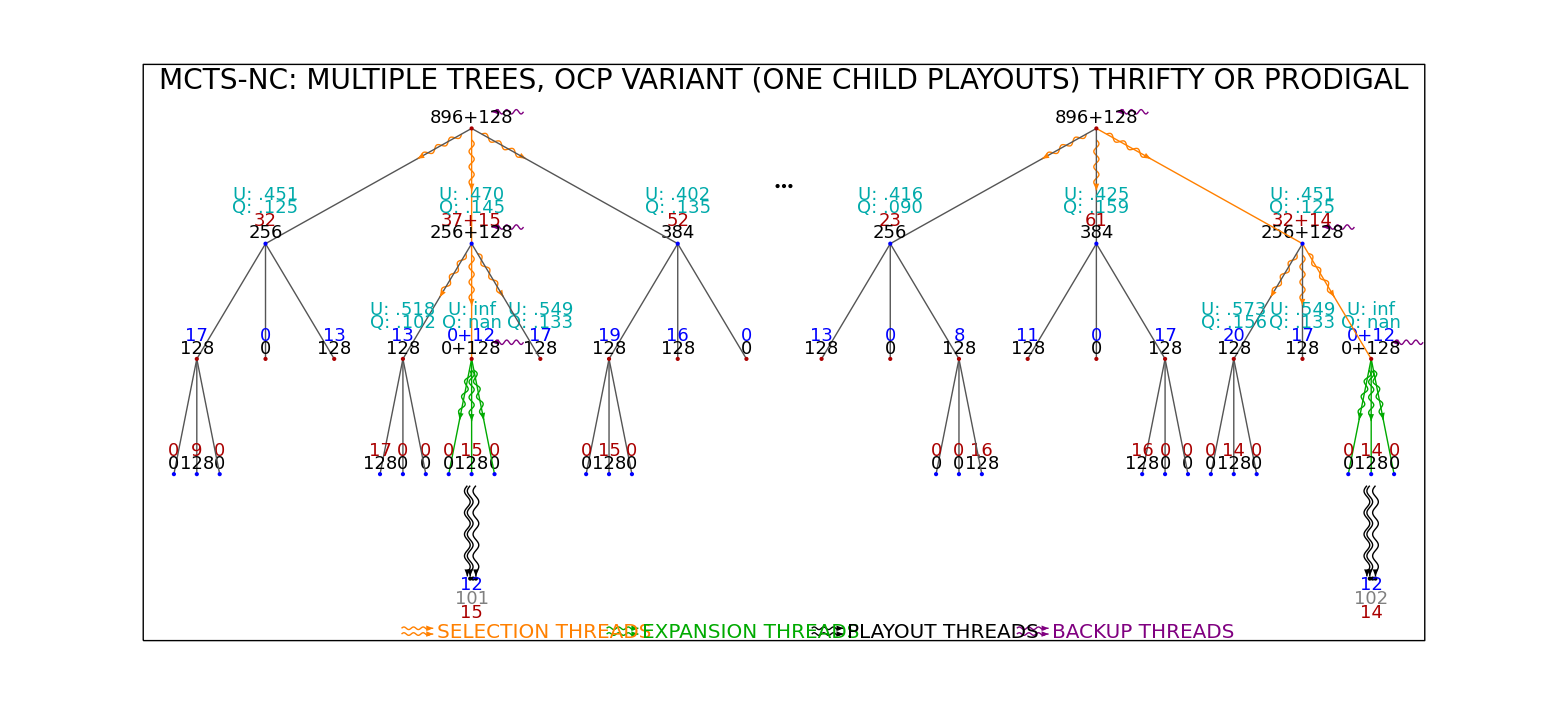

```mathematica
graphics=DrawMCTSCuda[json,True,""];
show=Show[Graphics[graphics],ImageSize->72 24]
```

```mathematica
p="C:\\Users\\klesk\\workspace\\mcts_numba_cuda\\extras\\";
Export[p<>f<>".pdf",show]
Export[p<>f<>".eps",show]
```

C:\Users\klesk\workspace\mcts_numba_cuda\extras\mctsnc_ocp_thrifty_fakegame_8steps.pdf

C:\Users\klesk\workspace\mcts_numba_cuda\extras\mctsnc_ocp_thrifty_fakegame_8steps.eps